## Conventional poverty trap

```mathematica
A=10;
α1=0.4;
s1=0.1;
s2=0.2;
s3=10;
d=2;
δP=0.5;
n=0.5;
```

```mathematica
f[kP_]:=A kP^α1;
sf[kP_]:=s1+(s2-s1)/(1+ⅇ^(-s3 (kP-d)));
```

```mathematica
Savings:=sf[kP] f[kP]
Depreciation:=(δP+n) kP
```

Find equilibrium points

```mathematica
kPEq=NSolve[Savings==Depreciation && 0 ≤kP≤4,kP];
```

```mathematica
kPList=kP/.%
```

{0.,1.00008,2.00769,3.17478}

```mathematica
yValues={};
Do[AppendTo[yValues,sf[i] f[i]],{i,kPList}]
```

```mathematica
print[yValues]
```

print[{0.,1.00008,2.00769,3.17478}]

Plot conventional poverty trap

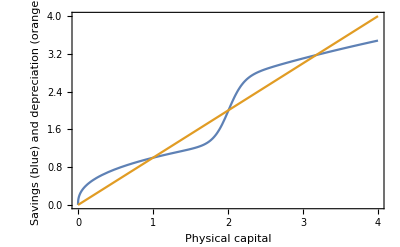

```mathematica
Plot[{Savings,Depreciation}, {kP,0,4}, 
Frame->True, FrameLabel->{"Physical capital", "Savings (blue) and depreciation (orange)"}]
```

## Physical and natural capital

```mathematica
α2 = 0.4;
δN = 1;
b=10;
H=1.5;
c1=1;
c2=0.5;
q=0.6;
```

```mathematica
Ef[KN_]:=q KN^α2
G[KN_]:=(b KN^2)/(H^2+KN^2)
L[kP_]:=1/(1+c1 kP^c2)
```

```mathematica
dkPdt:=sf[kP] Ef[KN] f[kP]-(δP+n) kP
dKNdt:=G[KN] L[kP]-δN KN
```

Find equilibrium points

```mathematica
EqPoints=Solve[{dkPdt==0,dKNdt==0 &&0<=kP≤4&&0<=KN≤5},{kP,KN},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{kP→0,KN→0},{kP→0,KN→0.230304},{kP→0.210189,KN→0.345571},{kP→1.13309,KN→4.32345},{kP→2.0161,KN→3.4872},{kP→2.80753,KN→2.98333}}

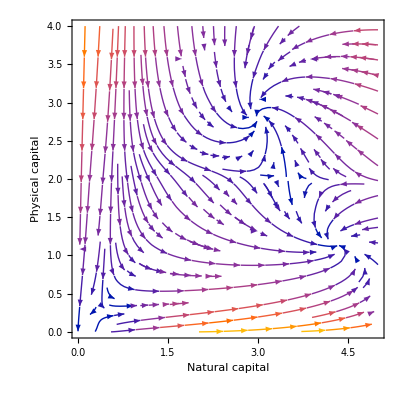

```mathematica
StreamPlot[{dKNdt,dkPdt},{KN,0,5},{kP,0,4}, 
Frame->True, FrameLabel->{"Natural capital", "Physical capital"}]
```

## Physical, natural and cultural capital

```mathematica
T0 =0.35;
P0=2;
PN=2.5;
δC=0.5;
```

```mathematica
P[KN_]=(P0 KN)/(PN+KN);
T[KC_]=T0 KC;
```

```mathematica
dkPdt:=sf[kP] Ef[KN] f[kP]-(δP+n)kP
dKNdt:=T[KC] G[KN] L[kP] -δN KN
dKCdt:=P[KN]-δC KC
```

```mathematica
(* EqPoints=NSolve[{dkPdt==0,dKNdt==0,dKCdt==0 && 0≤kP≤5 && 0≤KN≤5&& 0≤KC≤5},{kP,KN,KC},Reals] *)
```

```mathematica
Show[VectorPlot3D[{dKCdt, dKNdt,dkPdt},{KC,0,5},{KN,0,5},{kP,0,5}, 
AxesLabel->{"Cultural  capital", "Natural  capital", "Physical  capital"},
VectorAspectRatio->0.1,
VectorSizes->0.8,
VectorPoints->5],
Graphics3D[{PointSize[0.03],Point[{0,0,0}]}]]
```

-Graphics3D-

## Intensification trap model after transformation

```mathematica
ρ=0.5;
L2[kP_]:=ρ+(1-ρ)/(1+c1 kP^c2)
```

```mathematica
dkPdt:=sf[kP] Ef[KN] f[kP]-(δP+n)kP
dKNdt:=T[KC] G[KN] L2[kP] -δN KN
dKCdt:=P[KN]-δC KC
```

```mathematica
Show[VectorPlot3D[{dKCdt,dkPdt,dKNdt},{KC,0,5},{kP,0,5},{KN,0,10}, 
AxesLabel->{"Cultural  capital", "Physical  capital", "Natural  capital"},
BoxRatios->{1, 1, 2},
VectorAspectRatio->0.1,
VectorSizes->0.8,
VectorPoints->{4,4,8}],
Graphics3D[{PointSize[0.03],Point[{0,0,0}]}]
]
```

-Graphics3D-

## Subsistence trap model

```mathematica
s=0.2;
A=10;
q=0.6;
α1=0.4;
α2=0.4;
δP=0.5;
n=0.5;
r=0.2;
K=5;
D0=0.8;
D1=4;
D2=2.5;
```

```mathematica
G2[KN_]=r KN (K-KN);
Df[kP_]=D0/(1+ⅇ^(D1 (kP-D2)));
```

```mathematica
dkPdt:=s f[kP] Ef[KN]-(δP+n) kP
dKNdt:=G2[KN]-KN Df[kP]
```

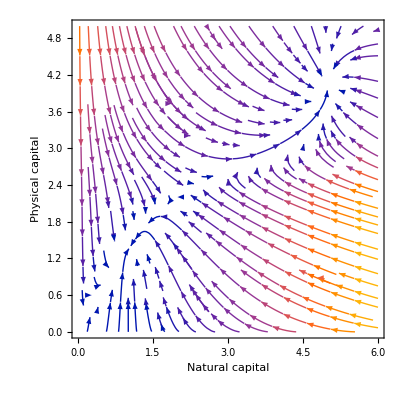

```mathematica
StreamPlot[{dKNdt,dkPdt},{KN,0,6},{kP,0,5}, 
Frame->True, FrameLabel->{"Natural capital", "Physical capital"}]
```